# Stokes 方程 管道中的流动

http://www.wolfram.com/mathematica/new-in-10/pdes-and-finite-elements/a-stokes-flow-in-a-channel.html

声明区域和流速场

## 管道缩紧

```mathematica
vfield=Through[{vx,vy}[x,y]];
Ω=ImplicitRegion[0≤x≤2&&0≤y≤0.5&&!(x≥1.3&&y≤0.1)&&!(x≥1&&y≥0.4),{x,y}];
RegionPlot[Ω,AspectRatio->Automatic,ImageSize->300]
```

-Graphics-

斯托克斯方程，但是(v.∇)v这一非线性项存在时 NDSolve 不能解……

```mathematica
stokeseqns=Inactivate@{ρ Grad[vfield,{x,y}].vfield==-Grad[p[x,y],{x,y}]+η Laplacian[vfield,{x,y}],Div[vfield,{x,y}]==0}
```

{ρ*{vx[x,y],vy[x,y]}{x,y}Inactive.{vx[x,y],vy[x,y]}==-1*p[x,y]{x,y}Inactive+η*{vx[x,y],vy[x,y]}{x,y}Inactive,{vx[x,y],vy[x,y]}{x,y}Inactive==0}

左端流入，右端压强恒定，其他边界上由于粘性，无速度。

```mathematica
boundarycond={DirichletCondition[vx[x,y]==4*0.3*y*(0.5-y)/(0.41)^2,x==0.],DirichletCondition[{vx[x,y]==0.,vy[x,y]==0.},0<x<2],DirichletCondition[p[x,y]==110.,x==2]};
```

```mathematica
vsol=NDSolve[{Activate@stokeseqns/.{ρ->0,η->1},boundarycond},{vx,vy,p},{x,y}∈Ω,Method->{"FiniteElement","InterpolationOrder"->{vx->2,vy->2,p->1}}]//First
```

{vx→InterpolatingFunction[…],vy→InterpolatingFunction[…],p→InterpolatingFunction[…]}

```mathematica
Show[RegionPlot[Ω,PlotStyle->Transparent],(*DensityPlot[p[x,y]/.vsol,{x,y}∈Ω],*)
StreamPlot[{vx[x,y],vy[x,y]}/.vsol,{x,y}∈Ω,StreamPoints->Fine],
AspectRatio->Automatic]
```

-Graphics-

## 绕球流动

```mathematica
vfield=Through[{vx,vy}[x,y]];
Ω=ImplicitRegion[0≤x≤10&&0≤y≤5&&((x-5)^2+(y-2.5)^2≥(.5)^2),{x,y}];
RegionPlot[Ω,AspectRatio->Automatic,ImageSize->300]
```

-Graphics-

注意！！！N-S 方程里的这一项一定要写成(∇v⃗)·v⃗,而不是 v⃗·(∇v⃗) ！！！否则虽然看起来很像，但是是错的。

```mathematica
stokeseqns=Inactivate@{ρ Grad[vfield,{x,y}].vfield==-Grad[p[x,y],{x,y}]+η Laplacian[vfield,{x,y}],Div[vfield,{x,y}]==0};
stokeseqns=Inactivate@{ρ vfield. Grad[vfield,{x,y}]==-Grad[p[x,y],{x,y}]+η Laplacian[vfield,{x,y}],Div[vfield,{x,y}]==0};
```

```mathematica
boundarycond=
{DirichletCondition[{vx[x,y]==y*(5-y),vy[x,y]==0},x==0.],
DirichletCondition[Thread[{vx[x,y],vy[x,y]}==20({{0, -1}, {1, 0}}).{x-5,y-2.5}],{x,y}∈Circle[{5,2.5},.5]],
DirichletCondition[{vx[x,y]==0.,vy[x,y]==0.},True],
DirichletCondition[p[x,y]==0.,x==10]};
```

```mathematica
vsol=NDSolve[{Activate@stokeseqns/.{ρ->1,η->1},boundarycond},{vx,vy,p},{x,y}∈Ω,Method->{"FiniteElement","InterpolationOrder"->{vx->2,vy->2,p->1},"MeshOptions"->{"IncludePoints"->{{0.15,0.2},{0.25,0.2}},AccuracyGoal->5,PrecisionGoal->5}}]//First;
```

```mathematica
Show[RegionPlot[Ω,PlotStyle->Transparent],(*DensityPlot[Evaluate[p[x,y]/.vsol],{x,y}∈Ω],*)
StreamPlot[Evaluate[{vx[x,y],vy[x,y]}/.vsol],{x,y}∈Ω,StreamPoints->Fine],
AspectRatio->Automatic]
```

-Graphics-

## 绕球流动 含时

```mathematica
vfield=Through[{vx,vy}[x,y,t]];
Ω=ImplicitRegion[0≤x≤10&&0≤y≤5&&((x-5)^2+(y-2.5)^2≥(.5)^2),{x,y}];
RegionPlot[Ω,AspectRatio->Automatic,ImageSize->300]
```

-Graphics-

```mathematica
stokeseqns=Inactivate@{ρ( vfield.Grad[vfield,{x,y}])==-Grad[p[x,y],{x,y}]+η Laplacian[vfield,{x,y}],Div[vfield,{x,y}]==0};
```

```mathematica
boundarycond=
{DirichletCondition[{vx[x,y]==y*(5-y),vy[x,y]==0},x==0.],
DirichletCondition[Thread[{vx[x,y],vy[x,y]}==20({{0, -1}, {1, 0}}).{x-5,y-2.5}],{x,y}∈Circle[{5,2.5},.5]],
DirichletCondition[{vx[x,y]==0.,vy[x,y]==0.},True],
DirichletCondition[p[x,y]==0.,x==10]};
```

```mathematica
vsol=NDSolve[{Activate@stokeseqns/.{ρ->1,η->1*^-3},boundarycond},{vx,vy,p},{x,y}∈Ω,Method->{"FiniteElement","InterpolationOrder"->{vx->2,vy->2,p->1},"MeshOptions"->{"IncludePoints"->{{0.15,0.2},{0.25,0.2}},AccuracyGoal->5,PrecisionGoal->5}}]//First;
```

FindRoot::dfmin: The minimal damping factor of 1/10000 has been reached.

```mathematica
Show[RegionPlot[Ω,PlotStyle->Transparent],(*DensityPlot[p[x,y]/.vsol,{x,y}∈Ω],*)
StreamPlot[Evaluate[{vx[x,y],vy[x,y]}/.vsol],{x,y}∈Ω,StreamPoints->Fine],
AspectRatio->Automatic]
```

-Graphics-

## 管道初始有进有出

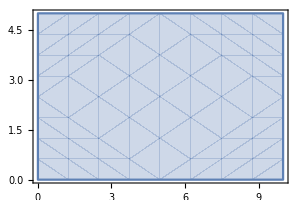

```mathematica
vfield=Through[{vx,vy}[x,y]];
Ω=ImplicitRegion[0≤x≤10&&0≤y≤5(*&&((x-5)^2+(y-2.5)^2≥(.5)^2)*),{x,y}];
RegionPlot[Ω,AspectRatio->Automatic,ImageSize->300]
```

```mathematica
stokeseqns=Inactivate@{ρ vfield.Grad[vfield,{x,y}]==-Grad[p[x,y],{x,y}]+η Laplacian[vfield,{x,y}],Div[vfield,{x,y}]==0};
```

```mathematica
boundarycond=
{DirichletCondition[{vx[x,y]==If[2≤y≤3,1,-1/8],vy[x,y]==0},x==0.],
DirichletCondition[{vx[x,y]==0.,vy[x,y]==0.},True],
DirichletCondition[p[x,y]==0.,x==10]};
```

```mathematica
vsol=NDSolve[{Activate@stokeseqns/.{ρ->0,η->1},boundarycond},{vx,vy,p},{x,y}∈Ω,Method->{"FiniteElement","InterpolationOrder"->{vx->2,vy->2,p->1}}]//First;
```

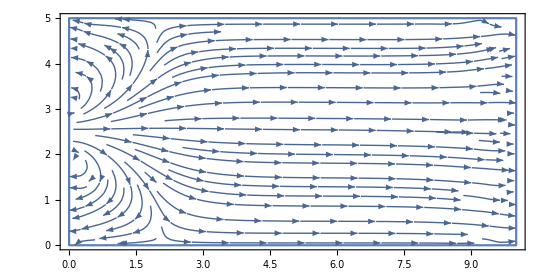

```mathematica
Show[RegionPlot[Ω,PlotStyle->Transparent],(*DensityPlot[p[x,y]/.vsol,{x,y}∈Ω],*)
StreamPlot[{vx[x,y],vy[x,y]}/.vsol,{x,y}∈Ω,StreamPoints->Fine],
AspectRatio->Automatic]
```

## 管道初始有进有出

```mathematica
vfield=Through[{vx,vy}[x,y]];
Ω=ImplicitRegion[0≤x≤10&&0≤y≤5(*&&((x-5)^2+(y-2.5)^2≥(.5)^2)*),{x,y}];
RegionPlot[Ω,AspectRatio->Automatic,ImageSize->300]
```

-Graphics-

```mathematica
stokeseqns=Inactivate@{ρ  vfield.Grad[vfield,{x,y}]==-Grad[p[x,y],{x,y}]+η Laplacian[vfield,{x,y}],Div[vfield,{x,y}]==0};
```

```mathematica
boundarycond=
{DirichletCondition[{vx[x,y]==If[2≤y≤3,1,-1/8],vy[x,y]==0},x==0.],
DirichletCondition[{vx[x,y]==0.,vy[x,y]==0.},True],
DirichletCondition[p[x,y]==0.,x==10]};
```

```mathematica
vsol=NDSolve[Activate@{stokeseqns/.{ρ->0,η->1},boundarycond},{vx,vy,p},{x,y}∈Ω,Method->{"FiniteElement","InterpolationOrder"->{vx->2,vy->2,p->1}}]//First;
```

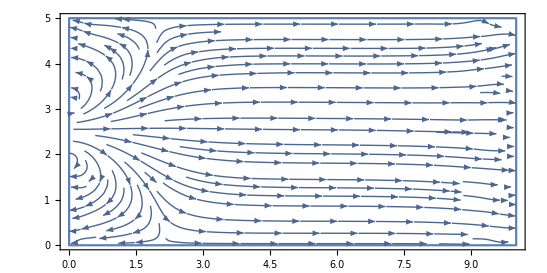

```mathematica
Show[RegionPlot[Ω,PlotStyle->Transparent],(*DensityPlot[p[x,y]/.vsol,{x,y}∈Ω],*)
StreamPlot[{vx[x,y],vy[x,y]}/.vsol,{x,y}∈Ω,StreamPoints->Fine],
AspectRatio->Automatic]
```

```mathematica
Curl[vfield,{x,y}]
```

-vx^(0,1)[x,y]+vy^(1,0)[x,y]

```mathematica
Curl[Flatten@{vfield,0},{x,y,z}]×Flatten@{vfield,0}
```

{vy[x,y] vx^(0,1)[x,y]-vy[x,y] vy^(1,0)[x,y],-vx[x,y] vx^(0,1)[x,y]+vx[x,y] vy^(1,0)[x,y],0}